## RBSim` Documentation

### Preamble

```mathematica
Needs["RBSim`"]
```

The following packages are needed to run some code found in this documentation notebook.

### Source Code

Open Source Code

## Introduction and Overview

This package provides generic tools for simulating Randomized Benchmarking (RB) and related protocols. Though RB is in the title of this package, it should be general enough to simulate any kind of protocol which relies on a gate set whose gates are specified by pulses.
The main advantage of this library is that it allows a wide class of error models. In particular, all of the following error models can be incorporated simultaneously:
    • Discrete error channels following any pulse, which may be gate dependent, independent, or depend on exactly which pulses preceded the present pulse.
    • Hardware distortions (for example, from a transfer function) applied to the entire concatenated pulse train of a given pulse sequence.
    • Coupling to an external quantum system.
    • Additive stochastic Hamiltonian noise, including on the bath.
    • Static parameter noise; noise chosen randomly at the beginning of each pulse sequence, but fixed for the duration of the sequence.

#### References

## Gate Sets

Pulses are generally stored in one of two formats. First, and more basic, is as a matrix of time step lengths and amplitudes of the form {{dt1,a11,a12,...},{dt2,a21,a22,...},{dt3,a31,a32,...},...} as used, for example, in the initialGuess argument to FindPulse. 
The second format, Pulse objects, are explained below and contain metadata such as Hamiltonians and distortion operators. This is the format output by FindPulse.

Pulse is a Head to store the output of FindPulse containing a list of rules from keys to values. For example, the output of FindPulse might be 
p=Pulse[TimeSteps->{0.1,0.1,0.1},Pulse->{{1,2},{2,0},{3,1}},UtilityValue->0.9994,...].

Retreiving Values
Like an Association, values of keys can be retreived by calling the key: p[TimeSteps]

Notes
• Pulse objects can be visualized using PulsePlot.
• Pulse serves an alternate role as a key to the pulse amplitudes of the solution found by FindPulse.

Possible Keys
UtilityValue
PenaltyValue
TimeSteps
Pulse
Target
ControlHamiltonians
InternalHamiltonian
DistortionOperator
PulsePenalty
ParameterDistribution
AmplitudeRange
ExitMessage

### Pulse Object Keys

UtilityValue is a key for Pulse whose value is the utility function value of the solution found by FindPulse.

PenaltyValue is a key for Pulse whose value is the PenaltyFunction value of the solution found by FindPulse.

TimeSteps is a key for Pulse whose value is a list of time step lengths for the solution found by FindPulse.

Pulse is a valid key for Pulse  which stores the amplitudes of the pulse.

Target is a key for Pulse whose value is the target entered as an argument to FindPulse.

ControlHamiltonians is a key for Pulse whose value is the list Hcontrol entered as an argument to FindPulse.

InternalHamiltonian is a key for Pulse whose value is the Hamiltonian Hint entered as an argument to FindPulse.

DistortionOperator is a valid key for Pulse which stores the distortion operator that acts on the input pulse.

PulsePenalty is a valid key for Pulse which stores the penalty function.

ParameterDistribution is a valid key for Pulse  which stores the distribution of parameters.

AmplitudeRange is a key for Pulse whose value is the amplitudeRange entered as an argument to FindPulse.

ExitMessage is a key for Pulse whose value is the exit message of FindPulse.

### Pulse Key Modification

PulseRemoveKeys[pulse,key1,key2,...] returns a new Pulse object with the given keys and their values removed from the Pulse object pulse.

PulseReplaceKey[pulse,key,newval] returns a new Pulse object with the value of the given key replaced with newval in the Pulse object pulse.

PulseHasKey[pulse,key] returns True iff key is one of the keys of pulse.

### Pulse Conversion and Transformation

SimForm[pulse,distort] converts a Pulse object pulse into the ShapedPulseQ format accepted by QSim`s PulseSim. If the optional argument distort is True (default value),  the DistortionOperator is called on the pulse.

ToPulse[pulsemat] turns the matrix pulsemat of the form {{dt1,a11,a12,...},{dt2,a21,a22,...},{dt3,a31,a32},...} into a Pulse object where all keys besides Pulse and TimeSteps are set to nominal qubit values.

Options
ToPulse accepts any of the following options whose values will override the default nominal values, for example, ToPulse[...,InternalHamiltonian->TP[X],...]
UtilityValue, PenaltyValue, Target, ControlHamiltonians, InternalHamiltonian, DistortionOperator, PulsePenalty, ParameterDistribution, AmplitudeRange, ExitMessage

FromPulse[pulse] turns the Pulse object pulse into a pulse matrix with format {{dt1,a11,a12,...},{dt2,a21,a22,...},{dt3,a31,a32},...}.

AddTimeSteps[dts,amplitudes] returns a pulse matrix with given time steps and amplitudes.

SplitPulse[pulseMat] returns {pulseMat⟦All,1⟧,pulseMat⟦All,2;;-1⟧}.

#### Example

```mathematica
pulsemat={{1,1,1},{2,3,4},{5,6,7}};
```

```mathematica
ToPulse[pulsemat]
```

Head | Value
UtilityValue | None
PenaltyValue | 0
ExitMessage | Generated by ToPulse.
Target | (1 | 0
0 | 1)
InternalHamiltonian | (0 | 0
0 | 0)
ControlHamiltonians | (0 | π
π | 0),(0 | -ⅈ π
ⅈ π | 0)
AmplitudeRange | {{-1,1},{-1,1}}
TimeSteps | {1,2,5}
Pulse | (1 | 3 | 6
1 | 4 | 7)
ParameterDistribution | None
DistortionOperator | IdentityDistortion[]
PulsePenalty | ZeroPenalty[]

```mathematica
FromPulse[ToPulse[pulsemat]]
```

{{1,1,1},{2,3,4},{5,6,7}}

```mathematica
SimForm[ToPulse[pulsemat]]
```

{{{1,1,1},{2,3,4},{5,6,7}},{{{0,2 π},{2 π,0}},{{0,-2 ⅈ π},{2 ⅈ π,0}}}}

### Pulse Manipulation

PulsePhaseRotate[pulse,ϕ] returns a new Pulse object where the phase between the amplitudes of the Pulse object pulse are rotated by a constant angle ϕ (radians). It is assumed that there are two amplitude values per time step.

PulsePhaseRamp[pulse,f] returns a new Pulse object where the pulse has been phase ramped with a slope 2π*f. The pulse is assumed to have two amplitudes per step, and is in x-y coordinates.

PulseModulate[pulse,f] returns a new Pulse object where the pulse has been cosine modulated at an angular frequency 2π*f. The pulse is assumed to have two amplitudes per step, and is in x-y coordinates.
PulseModulate[pulse,f,ϕ] returns a new Pulse object where the pulse has been modulated at an angular frequency 2π*f and a modulation phase ϕ. Here, ϕ=0 is equivalent to cosine modulation, and ϕ=π/2 is equivalent to sine modulation.

PulseDivide[pulse,n] returns a new Pulse object where each time step has been evenly divided into n steps.

#### Example 1

Rotate a pulse with Gaussian tails by angle π/4.

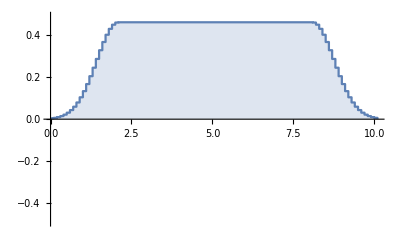
-Graphics--Graphics-

```mathematica
PulsePhaseRotate[GaussianTailsPulse[0.1,10,2,Area->5]//ToPulse,π/4]//PulsePlot
```

#### Example 2

Phase ramp a pulse with Gaussian tails by a frequency of 0.5.

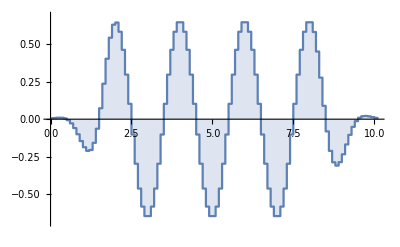
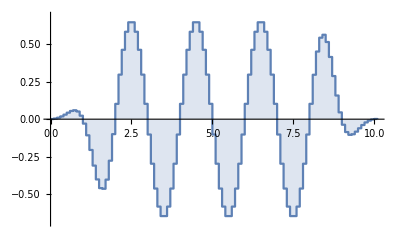

```mathematica
PulsePhaseRamp[GaussianTailsPulse[0.1,10,2,Area->5]//ToPulse,.5]//PulsePlot
```

#### Example 3

Define a square pulse with a parameter specifying offset frequency in the internal hamiltonian, and a target which wants to invert the populations of the |0⟩ and |1⟩ states.

```mathematica
pulseFn[amp_]:=PulseDivide[ToPulse[
{{.5,amp,0}},
InternalHamiltonian->2π δω Spin[Z][1/2],
Target->CoherentSubspaces[{({{1}, {0}}),({{0}, {1}})},{({{0}, {1}}),({{1}, {0}})}]
],100];
```

Plot the ability to invert population as a function of offset frequency. We see that:
• Square pulse does best at 0 offset, as expected.
• Phase ramping moves the peak to the right by 5 units.
• Modulating by 3 moves the peak to positive and negative 3. Note that we need to double the power.

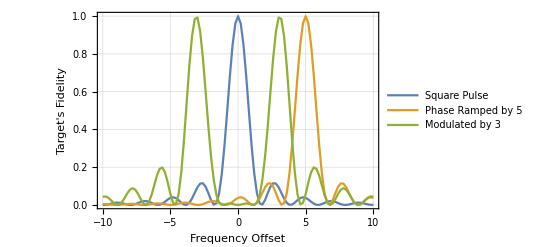

```mathematica
RobustnessPlot[{pulseFn[1],PulsePhaseRamp[pulseFn[1],5],PulseModulate[pulseFn[2],3]},δω->{-10,10,.2},{},
Joined->True,PlotRange->{0,1},LogPlot->False,PlotLegends->{"Square Pulse","Phase Ramped by 5","Modulated by 3"},FrameLabel->{"Frequency Offset","Target's Fidelity"},PlotTheme->"Detailed"
]
```

#### Example 4

Make a pulse with two time steps.

```mathematica
pulse=ToPulse[{{1,2,3},{4,5,6}}];
```

Divide each time step into ten pieces.

```mathematica
pulse[TimeSteps]
PulseDivide[pulse,10][TimeSteps]
```

{1,4}

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5}

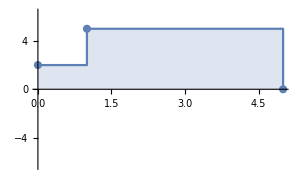
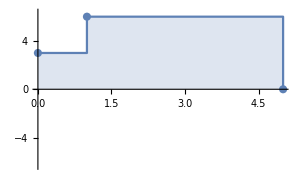

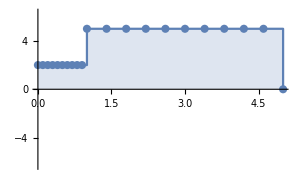
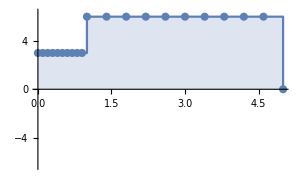

```mathematica
PulsePlot[pulse,ImageSize->300,Mesh->Full]
PulsePlot[PulseDivide[pulse,10],ImageSize->300,Mesh->Full]
```

### Pulse Matrix Generation

RandomPulse[dts,controlRange] returns a pulse matrix with given time steps dts and amplitudes chosen uniformly at random from the given controlRange.
RandomPulse[dt,n,controlRange] returns a pulse matrix with n time steps of length dt and amplitudes chosen uniformly at random from the given controlRange.

RandomSmoothPulse[dts,controlRange] returns a pulse matrix with given time steps dts and amplitudes with a smooth profile with limits set by controlRange.
RandomSmoothPulse[dt,n,controlRange] returns a pulse matrix with n time steps of length dt and amplitudes with a smooth profile with limits set by controlRange.

Options
InterpolationPoints, by default 10, specifies the interval at which random amplitudes are chosen. The intermediate amplitudes are interpolated with a spline.

GenerateAnnealedPulse[originalPulse,controlRange] returns a pulse that perturbs originalPulse by a new random pulse with limits set by controlRange.

Options
AnnealingGenerator specifies the function to use that generates random pulses. The default is RandomPulse.

GaussianTailsPulse[dt,T,riseTime,Area→A] returns a pulse matrix with a flat top and Gaussian tails. This pulse has two control channels and stepsize dt, total time T (rounded to the nearest dt), total area A, and tails each with length riseTime.
GaussianTailsPulse[dt,T,riseTime,Max→max] returns a pulse matrix with a flat top and Gaussian tails. This pulse has two control channels and stepsize dt, total time T (rounded to the nearest dt), maximum value max, and tails each with length riseTime.

#### Options

AnnealingGenerator is an option for GenerateAnnealPulse which specifies the function to use that generates random pulses.

#### Example 1

Generate a few random pulses.

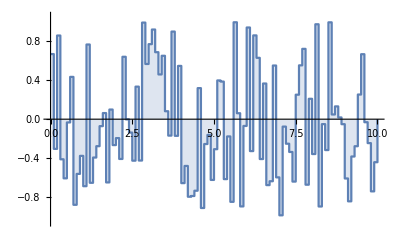
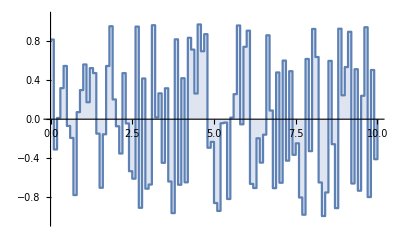

```mathematica
RandomPulse[.1,100,{{-1,1},{-1,1}}]//ToPulse//PulsePlot
```

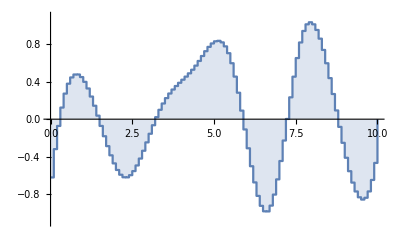
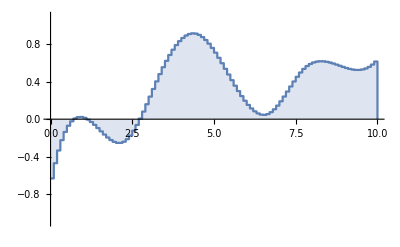

```mathematica
RandomSmoothPulse[.1,100,{{-1,1},{-1,1}}]//ToPulse//PulsePlot
```

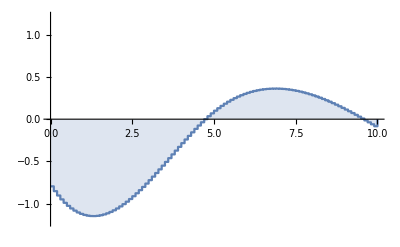
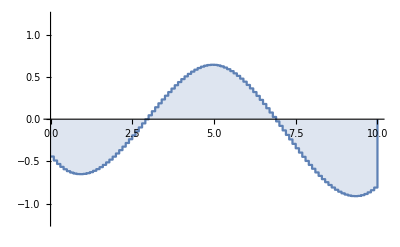

```mathematica
RandomSmoothPulse[.1,100,{{-1,1},{-1,1}},InterpolationPoints->50]//ToPulse//PulsePlot
```

#### Example 2

Anneal a pulse with 10% random fluctuations.

```mathematica
origPulse=RandomSmoothPulse[0.1,100,{{-1,1},{-1,1}}];
newPulse=GenerateAnnealedPulse[origPulse,0.1*{{-1,1},{-1,1}}];
```

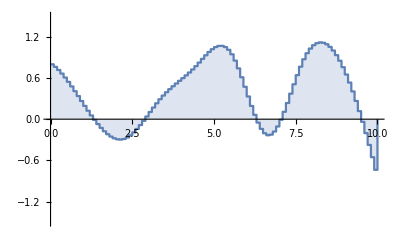
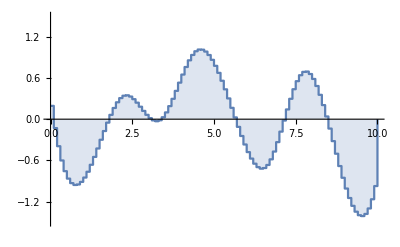

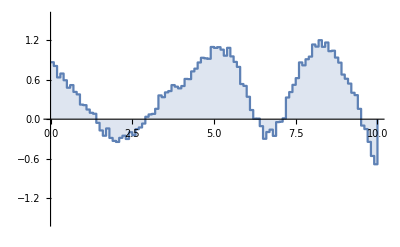
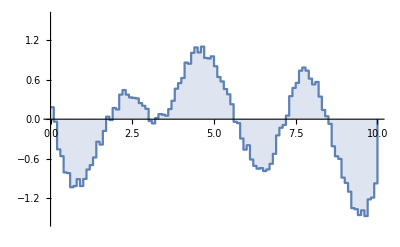

```mathematica
origPulse//ToPulse//PulsePlot
newPulse//ToPulse//PulsePlot
```

#### Example 3

Gaussian tails with total area of 5.

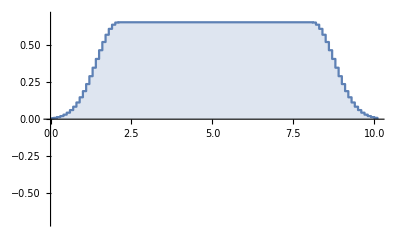
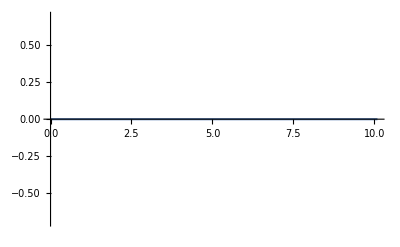

```mathematica
GaussianTailsPulse[0.1,10,2,Area->5]//ToPulse//PulsePlot
```

Gaussian tails with maximum amplitude of 5.

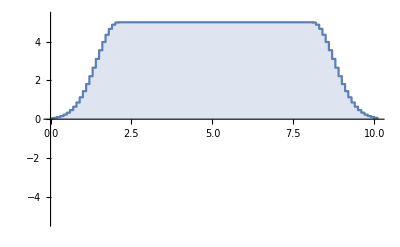
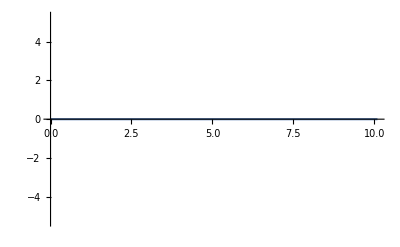

```mathematica
GaussianTailsPulse[0.1,10,2,Max->5]//ToPulse//PulsePlot
```

### Legalization and Normalization

LegalizePulse[pulseMat,controlRange] returns a new pulse matrix where the pulse amplitudes in the pulse matrix pulseMat have been clipped to the limits given in controlRange.
LegalizePulse[profile][pulseMat,controlRange] returns a new pulse matrix where the pulse amplitudes in the pulse matrix pulseMat have been clipped to the limits given in controlRange, multiplied by the value of the profile value at the given time step. The profile argument should be a list with the same length as pulseMat. Note that the profile can be a 1D array, in which case each control channel will see the same profile, or an array whose second dimension equals the number of control channels, in which cas each control channel may see a different profile.

LegalizeQuadraturePulse[Rmax][pulseMat,controlRange] returns a new pulse matrix where the norm of each timestep is clipped to lie between 0 and Rmax. Note that the input controlRange is ignored.

NormalizePulse[pulse,controlRange] scales and translates the pulse amplitues in the pulse matrix pulseMat to the interval [0,1] using controlRange as a reference.

#### Example 1

Clip the first channel at amplitude 1, and the second channel at amplitude 1.5.

```mathematica
illegalPulse=RandomSmoothPulse[.1,100,{{-3,3},{-3,3}}];
legalPulse=LegalizePulse[illegalPulse,{{-1,1},{-1.5,1.5}}];
```

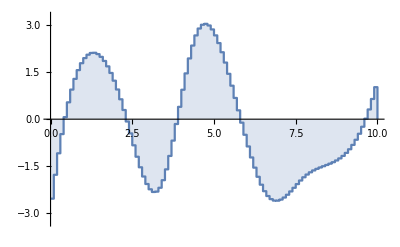
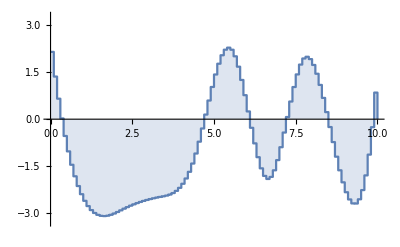

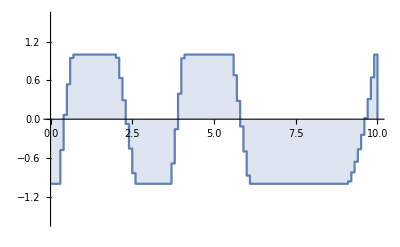
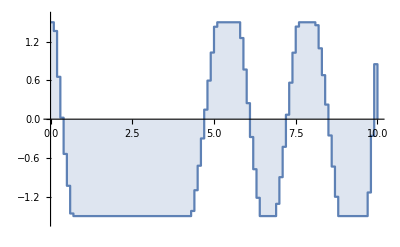

```mathematica
illegalPulse//ToPulse//PulsePlot
legalPulse//ToPulse//PulsePlot
```

#### Example 2

Use the GaussianTailsPulse function as a convenience function to create a 1D profile list.

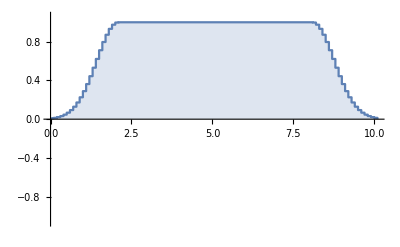
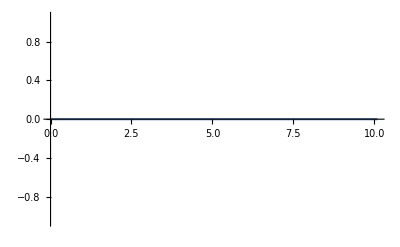

```mathematica
profile=GaussianTailsPulse[.1,.1*100,2,Max->1];
PulsePlot[ToPulse@profile]
profile=profile[[All,2]];
```

The pulse is now clipped to the shown profile

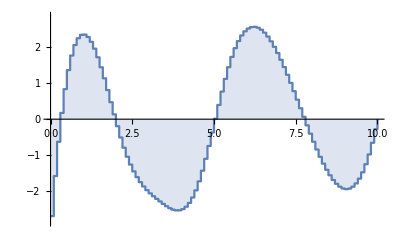
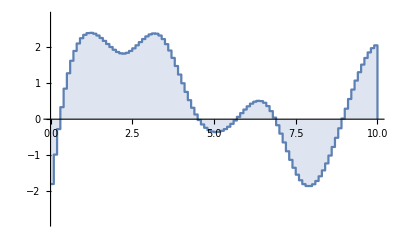

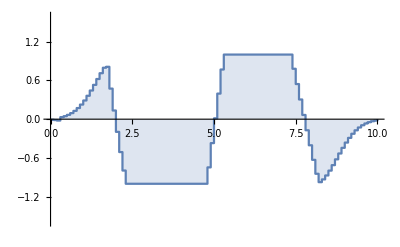
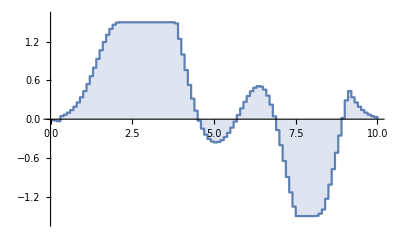

```mathematica
illegalPulse=RandomSmoothPulse[.1,100,{{-3,3},{-3,3}}];
legalPulse=LegalizePulse[profile][illegalPulse,{{-1,1},{-1.5,1.5}}];
illegalPulse//ToPulse//PulsePlot
legalPulse//ToPulse//PulsePlot
```

Note that if the profile can specify a different profile for each control channel.

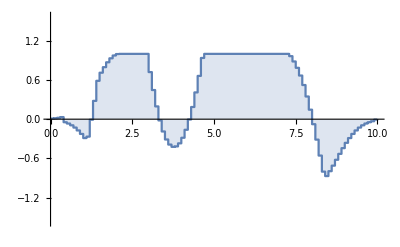
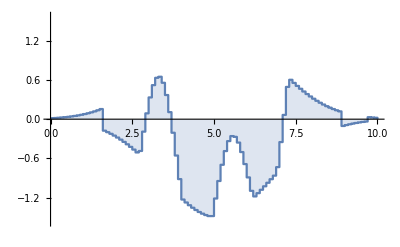

```mathematica
profile1=GaussianTailsPulse[.1,.1*100,2,Max->1];
profile2=GaussianTailsPulse[.1,.1*100,5,Max->1];
profile={profile1[[All,2]],profile2[[All,2]]}ᵀ;
legalPulse=LegalizePulse[profile][illegalPulse,{{-1,1},{-1.5,1.5}}];
legalPulse//ToPulse//PulsePlot
```

#### Example 3

Make a random pulse and then legalize it to two different radii. Everything is is cartesian coordinates.

```mathematica
illegalPulse=RandomSmoothPulse[.1,100,{{-10,10},{-10,10}}];
legalPulse1=LegalizeQuadraturePulse[1][illegalPulse,{}];
legalPulse2=LegalizeQuadraturePulse[7][illegalPulse,{}];
```

Make a distortion that converts to amplitude/phase so that we can clearly see the results.

```mathematica
distortion=VariableChangeDistortion[{Sqrt[x^2+y^2],ArcTan[x,y]},{x,y}];
```

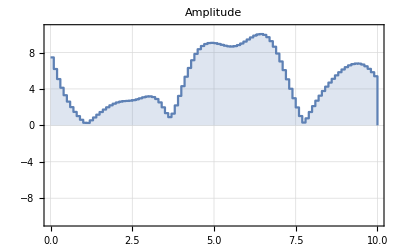
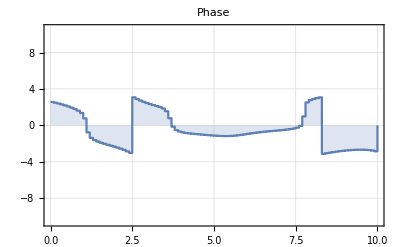

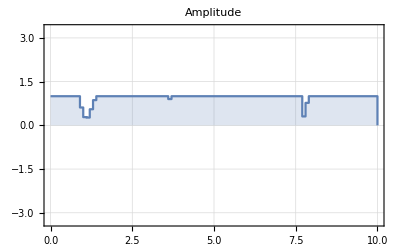
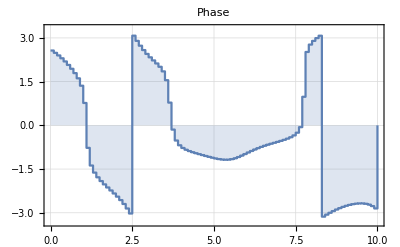

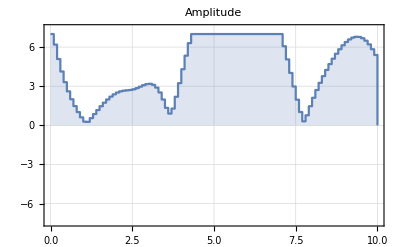
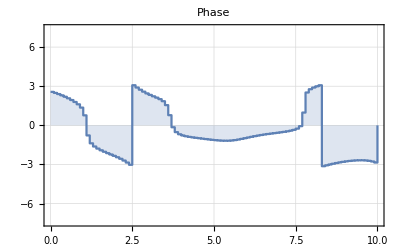

```mathematica
PulsePlot[distortion[illegalPulse,False]//ToPulse,PlotTheme->"Detailed",PlotLabel->DistributeOption["Amplitude","Phase"]]
PulsePlot[distortion[legalPulse1,False]//ToPulse,PlotTheme->"Detailed",PlotLabel->DistributeOption["Amplitude","Phase"]]
PulsePlot[distortion[legalPulse2,False]//ToPulse,PlotTheme->"Detailed",PlotLabel->DistributeOption["Amplitude","Phase"]]
```

#### Example 4

Clip the first channel at amplitude 1, and the second channel at amplitude 1.5.

```mathematica
abnormalPulse=RandomSmoothPulse[.1,100,{{-12,-10},{-4,5}}];
normalPulse=NormalizePulse[abnormalPulse,{{-12,-10},{-4,5}}];
```

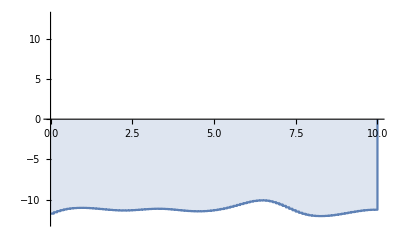
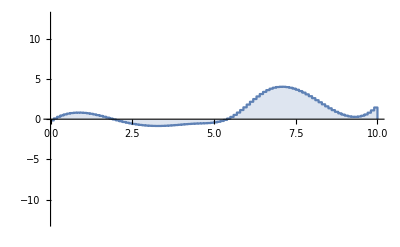

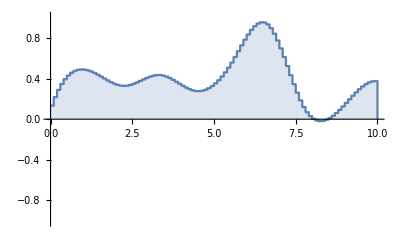
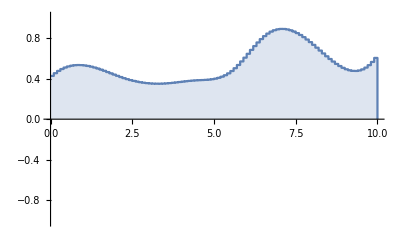

```mathematica
abnormalPulse//ToPulse//PulsePlot
normalPulse//ToPulse//PulsePlot
```